## Anharmonicity in string simulation

## Derivation of Equations of Motion

```mathematica
Clear[n]
Potential[springs_] :=k[1]Sum[(r[n-1]-r[n]).(r[n-1]-r[n]),{n,1,springs}]+k[2]Sum[Sin[θ[n]]^2,{n,1,springs-1}]
```

```mathematica
Potential[2];
TestPotential=%/.{θ[k_]->ArcCos[((r[k]-r[k-1]).(r[k+1]-r[k]))/(√((r[k]-r[k-1]).(r[k]-r[k-1]) (r[k+1]-r[k]).(r[k+1]-r[k])))]}/.{r[k_]->{x[k],y[k],z[k]}}//Simplify
```

k[2] (1-((x[0]-x[1]) (x[1]-x[2])+(y[0]-y[1]) (y[1]-y[2])+(z[0]-z[1]) (z[1]-z[2]))^2/(((x[0]-x[1])^2+(y[0]-y[1])^2+(z[0]-z[1])^2) ((x[1]-x[2])^2+(y[1]-y[2])^2+(z[1]-z[2])^2)))+k[1] ((x[0]-x[1])^2+(x[1]-x[2])^2+(y[0]-y[1])^2+(y[1]-y[2])^2+(z[0]-z[1])^2+(z[1]-z[2])^2)

```mathematica
PowerExpandTestPotential=Sum[D[TestPotential,{y[n][m],a}],{n,0,2},{m,1,3},{a,1,4}];
```

```mathematica
D[PowerExpandTestPotential,y[0]]
```

k[2] ((4 (-y[1][1]+y[2][1]) (1) ((-y[0][1]+y[1][1]) (-y[1][1]+y[2][1])+(-y[0][2]+y[1][2]) (-y[1][2]+y[2][2])+(-y[0][3]+y[1][3]) (-y[1][3]+y[2][3])))/(((-y[0][1]+y[1][1])^2+(-y[0][2]+y[1][2])^2+(-y[0][3]+y[1][3])^2) (((-1+1)^2+1^2+((11)^2))^2)-(2 2 1^2)/(1^2 1)-1+1+(2 1[1] (1))/(((1)^2+(1)^2+(1)^2) (1)))+52+1
 |  |  |  |

```mathematica
(*Sum[Series[TestPotential,{y[n][k],0,1}, Assumptions->{y[j_][i_]∈Reals, k[i_]>0}],{n,0,4},{k,1,3}]*)
```

2 k[1] (y[0][1]-y[1][1])-(2 ArcCos[((-y[0][1]+y[1][1]) (-y[1][1]+y[2][1])+(-y[0][2]+y[1][2]) (-y[1][2]+y[2][2])+(-y[0][3]+y[1][3]) (-y[1][3]+y[2][3]))/(√(((-y[0][1]+y[1][1])^2+(-y[0][2]+y[1][2])^2+(-y[0][3]+y[1][3])^2) ((-y[1][1]+y[2][1])^2+(-y[1][2]+y[2][2])^2+(-y[1][3]+y[2][3])^2)))] k[2] (((-y[0][1]+y[1][1]) ((-y[0][1]+y[1][1]) (-y[1][1]+y[2][1])+(-y[0][2]+y[1][2]) (-y[1][2]+y[2][2])+(-y[0][3]+y[1][3]) (-y[1][3]+y[2][3])) ((-y[1][1]+y[2][1])^2+(-y[1][2]+y[2][2])^2+(-y[1][3]+y[2][3])^2))/(((-y[0][1]+y[1][1])^2+(-y[0][2]+y[1][2])^2+(-y[0][3]+y[1][3])^2) ((-y[1][1]+y[2][1])^2+(-y[1][2]+y[2][2])^2+(-y[1][3]+y[2][3])^2))^(3/2)+(y[1][1]-y[2][1])/(√(((-y[0][1]+y[1][1])^2+(-y[0][2]+y[1][2])^2+(-y[0][3]+y[1][3])^2) ((-y[1][1]+y[2][1])^2+(-y[1][2]+y[2][2])^2+(-y[1][3]+y[2][3])^2)))))/(√(1-((-y[0][1]+y[1][1]) (-y[1][1]+y[2][1])+(-y[0][2]+y[1][2]) (-y[1][2]+y[2][2])+(-y[0][3]+y[1][3]) (-y[1][3]+y[2][3]))^2/(((-y[0][1]+y[1][1])^2+(-y[0][2]+y[1][2])^2+(-y[0][3]+y[1][3])^2) ((-y[1][1]+y[2][1])^2+(-y[1][2]+y[2][2])^2+(-y[1][3]+y[2][3])^2))))

## Simple Model - Two fixed springs connected to same mass

```mathematica
Clear["Global`*"];
```

```mathematica
KineticEnergy=1/2 m(vx^2+ vy^2);
PotentialEnergy=1/2 k1(√(x^2+y^2)-L1)^2+1/2 k2(√((x-Rx)^2+(y-Ry)^2)-L2)^2;
Lagrangian=KineticEnergy-PotentialEnergy
```

1/2 m (vx^2+vy^2)-1/2 k1 (-L1+√(x^2+y^2))^2-1/2 k2 (-L2+√((-Rx+x)^2+(-Ry+y)^2))^2

## Same springs and equilibrium distances

```mathematica
Lagrangian/.{k1->k,k2->k,L1->L,L2->L,Ry->0};
SimpleLagrangian=%;
```

```mathematica
(*LagrangesEquation[lagrangian_]:=
Module[{acceleration, force},
acceleration = D[
]*)
```

```mathematica
Eq1=D[D[SimpleLagrangian,vx]/.{vx->x'[t],vy->y'[t]},t]-(D[SimpleLagrangian,x]/.{x->x[t],y->y[t]})
Eq2=D[D[SimpleLagrangian,vy]/.{vx->x'[t],vy->y'[t]},t]-(D[SimpleLagrangian,y]/.{x->x[t],y->y[t]});
Eq1b=D[D[SimpleLagrangian,vx]/.{vx->x'[t],vy->y'[t]},t]-(D[(Series[SimpleLagrangian,{y,0,4}]//Normal),x]/.{x->x[t],y->y[t]})
Eq2b=D[D[SimpleLagrangian,vy]/.{vx->x'[t],vy->y'[t]},t]-(D[(Series[SimpleLagrangian,{y,0,4}]//Normal),y]/.{x->x[t],y->y[t]});
```

(k x[t] (-L+√(x[t]^2+y[t]^2)))/(√(x[t]^2+y[t]^2))+(k (-Rx+x[t]) (-L+√((-Rx+x[t])^2+y[t]^2)))/(√((-Rx+x[t])^2+y[t]^2))+m x''[t]

1/2 (-2 k Rx+(2 k L (Rx-x[t]))/(√((Rx-x[t])^2))+4 k x[t]-(2 k L x[t])/(√(x[t]^2)))-((k L (Rx-x[t]))/(2 ((Rx-x[t])^2)^(3/2))-(k L x[t])/(2 (x[t]^2)^(3/2))) y[t]^2-((k L)/(8 (Rx-x[t])^3 √((Rx-x[t])^2))-(k L √((Rx-x[t])^2))/(2 (Rx-x[t])^5)-(k L)/(8 x[t]^3 √(x[t]^2))+(k L √(x[t]^2))/(2 x[t]^5)) y[t]^4+m x''[t]

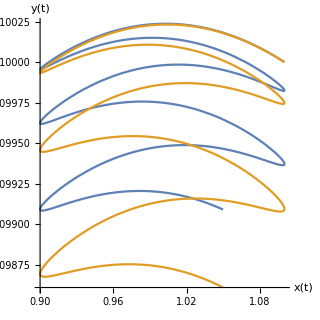

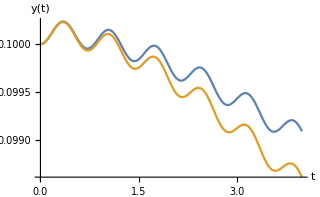

```mathematica
sol=NDSolve[
{Eq1==0,Eq2==0,x[0]==1.1,y[0]==0.1,x'[0]==0,y'[0]==0}/.{Rx->2,L->1,k->10,m->1},
{x,y},{t,4}];
solb=NDSolve[
{Eq1b==0,Eq2b==0,x[0]==1.1,y[0]==0.1,x'[0]==0,y'[0]==0}/.{Rx->2,L->1,k->10,m->1},
{x,y},{t,4}];
ParametricPlot[{Evaluate[{x[t],y[t]}/.sol],Evaluate[{x[t],y[t]}/.solb]},{t,0,4},PlotRange->Full,AxesLabel->{x[t],y[t]},AspectRatio->1]
Plot[{Evaluate[y[t]/.sol],Evaluate[y[t]/.solb]},{t,0,4},PlotRange->Full,AxesLabel->{t,y[t]}]
```

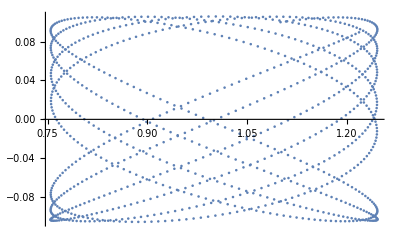

```mathematica
Table[Evaluate[{x[t],y[t]}/.sol][[1]],{t,0,10,0.01}];
ListPlot[%]
```

```mathematica
{Eq1,Eq2} - m{x''[t],y''[t]}//Simplify//MatrixForm
Collect[-%/.{Rx->2,L->1,k->10,m->1}/.{x[t]->1.1,y[t]->0.1},{x[t],y[t]}]//MatrixForm
```

((k (-Rx+x[t]) (-L+√((Rx-x[t])^2+y[t]^2)))/(√((Rx-x[t])^2+y[t]^2))+k x[t] (1-L/(√(x[t]^2+y[t]^2)))
k y[t] (2-L/(√(x[t]^2+y[t]^2))-L/(√(Rx^2-2 Rx x[t]+x[t]^2+y[t]^2))))

(-1.97991
0.00967272)

## Simple Model - arbitrary series of spring

```mathematica
Clear["Global`*"];
```

#### Define Lagrangian for arbitrary number of masses connected by strings and two fixed points

```mathematica
Lagrangian[masses_]:=
Module[{KineticEnergy, PotentialEnergy},
KineticEnergy=Sum[1/2 m[n](vx[n]^2+vy[n]^2),{n,1, masses}];
PotentialEnergy=1/2 k[1](√(x[1]^2+y[1]^2)-L[1])^2+Sum[1/2 k[n](√((x[n-1]-x[n])^2+(y[n-1]-y[n])^2)-L[n])^2,{n,2,masses}]+1/2 k[masses+1](√((x[masses]-Rx)^2+(y[masses]-Ry)^2)-L[masses+1])^2;
KineticEnergy-PotentialEnergy
]
```

#### Define equations of motion

```mathematica
LagrangesEquations[masses_,lagrangian_]:=Table[
{0==D[D[lagrangian,vx[n]]/.{vx[n]->D[x[n][t],t],vy[n]->D[y[n][t],t]},t]-(D[lagrangian,x[n]]/.{x[k_]->x[k][t],y[k_]->y[k][t]}),0==D[D[lagrangian,vy[n]]/.{vx[n]->D[x[n][t],t],vy[n]->D[y[n][t],t]},t]-(D[lagrangian,y[n]]/.{x[k_]->x[k][t],y[k_]->y[k][t]})},
{n,1,masses}]//Flatten
DependentVariableList[masses_]:=Table[{x[n],y[n]},{n,1,masses}]//Flatten
```

#### Initial Conditions

```mathematica
Lagrangian[10];
LagrangesEquations[10,%];
DependentVariableList[2];
```

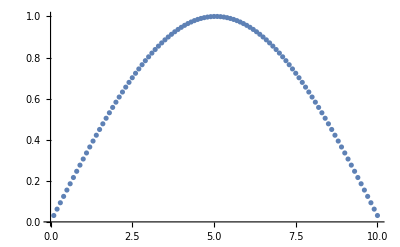

```mathematica
ListPlot[Table[{n/10,Sin[(n π)/101]},{n,1,100}]]
```

```mathematica
NN=100;
InitialConditions[masses_]:=Table[{x[n][0]==n/10,y[n][0]==Sin[(n π)/(masses+1)],x[n]'[0]==0.0,y[n]'[0]==0},{n,1,masses}];
solN=NDSolve[
Flatten[{LagrangesEquations[NN,Lagrangian[NN]],InitialConditions[NN](*,x[10][0]==9.5,y[10][0]==0.6,x[10]'[0]==0,y[10]'[0]==0*)}]/.{Rx->11,Ry->0}/.{L[k_]->0.0001,k[m_]->10,m[k_]->1},
DependentVariableList[NN],{t,0,100}];
PlottingFunctions = Table[Evaluate[{x[n][tt],y[n][tt]}/.solN][[1]],{n,1,NN}];
ParametricPlot[PlottingFunctions,{tt,0,100},PlotRange->{{-0,12},{-5,5}}]
Animate[ParametricPlot[PlottingFunctions,{tt,t-0.1,t+0.1},PlotRange->{{-1,12},{-1,1}}(*,AspectRatio->1*)],{t,0.5,99.5}]
```

-Graphics-